# NE352 Term Paper

## Chern-number calculator module

```mathematica
(*Chern number calculator credits: https://github.com/atom-sun/chern/*)
BeginPackage["ChernCalculator`"];
(*Exported symbols added here with SymbolName::usage*)
chern::usage="Chern number calculator for 2D materials.
    Input hamiltonian should be either
    1) bivariate function that generates a Hermitian matrix, like
      hk[kx_, ky_] := ({{1 - Cos[kx] - Cos[ky], Sin[kx] - I Sin[ky]},
          {Sin[kx] + I Sin[ky], -1 + Cos[kx] + Cos[ky]}})
      or
    2) some set-delayed expression that contains 'kx' and 'ky' (who are
      actually Global`kx, Global`ky), like
      hk := ({{1 - Cos[kx] - Cos[ky], Sin[kx] - I Sin[ky]},
          {Sin[kx] + I Sin[ky], -1 + Cos[kx] + Cos[ky]}})
    The former is preferred.
    ";

Begin["`Private`"];

chern[hamiltonian_,ndiscretized_:16]:=Module[{nQq=ndiscretized,hk=If[funcQ[hamiltonian],hamiltonian,(hamiltonian/.{Global`kx->#1,Global`ky->#2})&],qqx,qqy,hErg,hVec,cn},{qqx,qqy}=disCretize[nQq];
If[check[hk]===0,cn=ConstantArray[0,Length[hk@@{0.,0.}]],{hErg,hVec}=diagn[hk,qqx,qqy];cn=calcChern[hVec];];
cn];

check[hamiltonian_]:=Block[{$AssertFunction=Throw[{##}]&,kx,ky,hk,ndim},hk=hamiltonian@@{kx,ky};
ndim=Length[hk];
Assert[Dimensions[Dimensions[hk]]==={2},"input not matrix"];
Assert[Dimensions[hk][[2]]===ndim,"input not square matrix"];
Assert[AllTrue[hk@@{0,0},NumericQ,2],"NumericQ fails at {0,0}"];
Assert[Chop[ComplexExpand[hk-ConjugateTranspose[hk]]]===ConstantArray[0,{ndim,ndim}],"Not Hermitian matrix"];
If[Chop[ComplexExpand[hk-Transpose[hk]]]===ConstantArray[0,{ndim,ndim}],0,1]];

funcQ[_Function|_IntepolatingFunction|_CompiledFunction]:=True;
funcQ[f_Symbol]:=Or[DownValues[f]=!={},MemberQ[Attributes[f],NumericFunction]];
funcQ[_]:=False;

disCretize[nQq_]:=Module[{nQx=nQq,nQy=nQq,nqqx,dqx,qqx,nqqy,dqy,qqy},nqqx=nQx+1;
dqx=2.*π/nQx;
qqx=N[Table[(jqx-1.)*dqx-π,{jqx,1,nqqx}]];
nqqy=nQy+1;
dqy=2.*π/nQy;
qqy=N[Table[(jqy-1.)*dqy-π,{jqy,1,nqqy}]];
{qqx,qqy}];

diagn[hk_,qqx_,qqy_]:=Module[{nqqx=Length[qqx],nqqy=Length[qqy],kx,ky,hErg,hVec,hamilt,erg,vec,where},hErg=Table[Null,{jqy,1,nqqy},{jqx,1,nqqx}];
hVec=Table[Null,{jqy,1,nqqy},{jqx,1,nqqx}];
Table[kx=qqx[[jqx]];
ky=qqx[[jqy]];
hamilt=hk@@{kx,ky};
{erg,vec}=Eigensystem[N[hamilt]];
where=DeleteDuplicates[Flatten[Map[Position[erg,#]&,Sort[erg,Less]]]];
erg=erg[[where]];
vec=vec[[where]];
Part[hErg,jqy,jqx]=erg;
Part[hVec,jqy,jqx]=vec;,{jqy,nqqy},{jqx,nqqx}];
{hErg,hVec}];

calcChern[hVec_]:=Module[{cnlist=Table[0,Dimensions[hVec][[3]]],u12,u23,u34,u41,t12,t23,t34,t41,tplaquet,nqqy=Dimensions[hVec][[1]],nqqx=Dimensions[hVec][[2]]},Table[u12=Conjugate[hVec[[jqy,jqx+1]]].Transpose[hVec[[jqy,jqx]]];
u23=Conjugate[hVec[[jqy+1,jqx+1]]].Transpose[hVec[[jqy,jqx+1]]];
u34=Conjugate[hVec[[jqy+1,jqx]]].Transpose[hVec[[jqy+1,jqx+1]]];
u41=Conjugate[hVec[[jqy,jqx]]].Transpose[hVec[[jqy+1,jqx]]];
t12=DiagonalMatrix[Diagonal[u12]];
t23=DiagonalMatrix[Diagonal[u23]];
t34=DiagonalMatrix[Diagonal[u34]];
t41=DiagonalMatrix[Diagonal[u41]];
tplaquet=t41.t34.t23.t12;
cnlist+=Arg[Diagonal[tplaquet]];,{jqy,1,nqqy-1},{jqx,1,nqqx-1}];
cnlist/=2 π;
Chop[cnlist]];

End[]; (*`Private`*)

EndPackage[]
```

## Graphene-like semi metal model

```mathematica
Subscript[σ, z]={{1,0},{0,-1}};
Subscript[σ, x]={{0,1},{1,0}};
Subscript[σ, y]={{0, -I}, {I,0}};
II={{1,0},{0,1}};
a=1;
Subscript[t, 1]=1;
H0:=Subscript[t, 1] (Subscript[σ, x](Cos[a*kx]+Cos[Sqrt[3]/2 * a*ky-1/2 *a *kx]+Cos[-Sqrt[3]/2 * a*ky-1/2 *a *kx])-Subscript[σ, y] (Sin[a*kx]+Sin[Sqrt[3]/2 * a*ky-1/2 *a *kx]+Sin[-Sqrt[3]/2 * a*ky-1/2 *a *kx]))
```

```mathematica
E1:=Eigenvalues[H0][[1]];
E2:=Eigenvalues[H0][[2]];
```

```mathematica
Plot3D[{E1,E2}, {kx, -Pi/a,Pi/a }, {ky, -Pi/a, Pi/a}]
```

-Graphics3D-

## Deformation by Haldane mass term

```mathematica
H:= H0+(M+2 Subscript[t, 2] (Sin[kx*3/2 *a+Sqrt[3]/2 ky*a]+Sin[-kx*3/2 *a+Sqrt[3]/2 ky*a]+Sin[-ky*Sqrt[3]*a]))Subscript[σ, z]
```

```mathematica
E1:=Sort[Eigenvalues[H]][[1]];
E2:=Sort[Eigenvalues[H]][[2]];
```

```mathematica
(*Subscript[t, 2]/M > 0.19*)
M=0.7; Subscript[t, 1]=-1; Subscript[t, 2]=-0.24;
Plot3D[{E1,E2}, {kx, -Pi/a,Pi/a }, {ky, -Pi/a, Pi/a}]
```

-Graphics3D-

```mathematica
(*Subscript[t, 2]/M = 0.19*)
M=0.7; Subscript[t, 1]=-1; Subscript[t, 2]=-M/3/Sqrt[3];
Plot3D[{E1,E2}, {kx, -Pi/a,Pi/a }, {ky, -Pi/a, Pi/a}]
```

-Graphics3D-

```mathematica
(*Subscript[t, 2]/M < 0.19*)
```

```mathematica
M=0.7; Subscript[t, 1]=-1; Subscript[t, 2]=-M/6/Sqrt[3];
Plot3D[{E1,E2}, {kx, -Pi/a,Pi/a }, {ky, -Pi/a, Pi/a}]
```

-Graphics3D-

### Chern number calculation

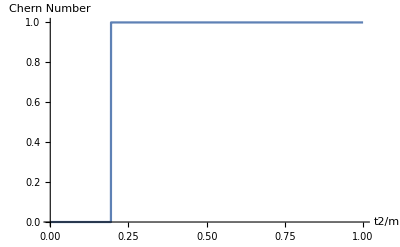

```mathematica
k:={kx/Sqrt[3],ky*2/3};
t1=1;
a1={Sqrt[3]/2,1/2};
a2={0,-1};
a3={-Sqrt[3]/2,1/2};
b1:=a2-a3;
b2:=a3-a1;
b3:=a1-a2;
hk:=2*t2*Cos[ϕ]*(Cos[k.b1]+Cos[k.b2]+Cos[k.b3])*PauliMatrix[0]+t1*((Cos[k.a1]+Cos[k.a2]+Cos[k.a3])*PauliMatrix[1]+(Sin[k.a1]+Sin[k.a2]+Sin[k.a3])*PauliMatrix[2])+(m-2*t2*Sin[ϕ]*(Sin[k.b1]+Sin[k.b2]+Sin[k.b3]))*PauliMatrix[3];

m=1;
ϕ=π/2;
hk//MatrixForm;

(*default discretization 16x16*)
Plot[chern[hk][[2]], {t2, 0, 1}, AxesLabel->{"t2/m", "Chern Number"}]
(*We can see that the chern number changes to 1, when t2/m > 1/(3√3)*)
```

## Two-band square lattice model

```mathematica
hk:=A Sin[kx] Subscript[σ, x]-A Sin[ky] Subscript[σ, y]+MM Subscript[σ, z];
MM:= M+2B(2-Cos[kx]-Cos[ky]);
k:={kx,ky};
A=1;
B=1;
E1:=Sort[Eigenvalues[hk]][[1]];
E2:=Sort[Eigenvalues[hk]][[2]];
```

```mathematica
(*M/B < 0*)
M=-5;
Plot3D[{E1,E2}, {kx, -Pi/a,Pi/a }, {ky, -Pi/a, Pi/a}]
```

-Graphics3D-

```mathematica
(*M/B = 0*)
M=0;
Plot3D[{E1,E2}, {kx, -Pi/a,Pi/a }, {ky, -Pi/a, Pi/a}]
```

-Graphics3D-

```mathematica
(*M/B >0*)
M=1;
Plot3D[{E1,E2}, {kx, -Pi/a,Pi/a }, {ky, -Pi/a, Pi/a}]
```

-Graphics3D-

### Chern number calculation

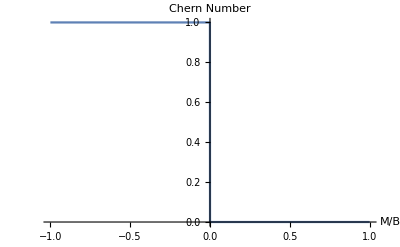

```mathematica
hk:=A Sin[kx] Subscript[σ, x]-A Sin[ky] Subscript[σ, y]+MM Subscript[σ, z];
MM:= M+2B(2-Cos[kx]-Cos[ky]);
k:={kx,ky};
A=1;
B=1;
Plot[chern[hk][[1]], {M, -1, 1}, AxesLabel->{"M/B", "Chern Number"}]
```